# Assemble sparse matrices from the matrix elements

Two different types of matrices are assembled:
1. The full matrix, all l,m included. This is used for time-dependent solutions.
2. The augmented matrix, only even l,m (due to symmetries in the Jeffery equations), and the l=0 mode removed and moved to the right hand side, such that the matrix equation is actually invertible.

NOTE: The optimizations in here are true not in general.
Even l,m : Due to symmetries in the Jeffery problem in shear flow
Conjugate matrixelementns upon Δm->-Δm because P is real-valued

## Matrix elements (taken from previous notebook)

These are the matrix elements from the previous file, just copied and pasted.

```mathematica
matrixelements={{{-4,0},1/(14 √5)√((1+2 l)/(-7+2 l)) stEff Λ^2 (Piecewise[{{1/2 √(35/2) (-3+l) (-2+l) (-1+l) √(l (-7+2 l)) √(1/(-630+2007 l-32 l^2-6363 l^3+9618 l^4-6552 l^5+2352 l^6-432 l^7+32 l^8)), l≥4}, {0, True}}]) (If[l≥4&&l+m>3,√(((-4+l)+(1+m)) ((-4+l)-(1+m)+1)),0] (Piecewise[{{-√(-49/2+7 l) √(((-4+l-m) (-3+l-m) (-2+l-m) (-1+l-m) (l-m) (-2+l+m) (-1+l+m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}])+If[l≥4&&3+m<l,√(((-4+l)-(-1+m)) ((-4+l)+(-1+m)+1)),0] (Piecewise[{{-√(-49/2+7 l) √(((-2+l-m) (-1+l-m) (l-m) (-4+l+m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}]))},{{-4,2},1/(28 √5)√((1+2 l)/(-7+2 l)) stEff Λ (1+Λ) (Piecewise[{{1/2 √(35/2) (-3+l) (-2+l) (-1+l) √(l (-7+2 l)) √(1/(-630+2007 l-32 l^2-6363 l^3+9618 l^4-6552 l^5+2352 l^6-432 l^7+32 l^8)), l≥4}, {0, True}}]) (√7 If[l≥4&&l+m>1,√(((-4+l)+(3+m)) ((-4+l)-(3+m)+1)),0] (Piecewise[{{-√(-7/2+l) √(((-6+l-m) (-5+l-m) (-4+l-m) (-3+l-m) (-2+l-m) (-1+l-m) (l-m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}])-2 √2 If[l≥4&&4+Abs[2+m]≤l,2+m,0] (Piecewise[{{1/2 √7 √(-7+2 l) √(((-5+l-m) (-4+l-m) (-3+l-m) (-2+l-m) (-1+l-m) (l-m) (-1+l+m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}])-If[l≥4&&5+m<l,√(((-4+l)-(1+m)) ((-4+l)+(1+m)+1)),0] (Piecewise[{{-√(-49/2+7 l) √(((-4+l-m) (-3+l-m) (-2+l-m) (-1+l-m) (l-m) (-2+l+m) (-1+l+m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}]))},{{-4,4},-1/(2 √35)√((1+2 l)/(-7+2 l)) stEff Λ^2 (Piecewise[{{1/2 √(35/2) (-3+l) (-2+l) (-1+l) √(l (-7+2 l)) √(1/(-630+2007 l-32 l^2-6363 l^3+9618 l^4-6552 l^5+2352 l^6-432 l^7+32 l^8)), l≥4}, {0, True}}]) (2 √2 If[l≥4&&4+Abs[4+m]≤l,4+m,0] (Piecewise[{{1/4 √(-7+2 l) √(((-7+l-m) (-6+l-m) (-5+l-m) (-4+l-m) (-3+l-m) (-2+l-m) (-1+l-m) (l-m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}])+If[l≥4&&7+m<l,√(((-4+l)-(3+m)) ((-4+l)+(3+m)+1)),0] (Piecewise[{{-√(-7/2+l) √(((-6+l-m) (-5+l-m) (-4+l-m) (-3+l-m) (-2+l-m) (-1+l-m) (l-m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}]))},{{-2,0},1/840 √((1+2 l)/(-3+2 l)) (-280 ⅈ If[l≥2&&2+Abs[m]≤l,m,0] (Piecewise[{{(-1+l) √(l (-9/2+3 l)) √(1/(-3+5 l+10 l^2-20 l^3+8 l^4)), l≥2}, {0, True}}]) (Piecewise[{{√(-9/2+3 l) √((l^2-2 l^3+l^4-m^2+2 l m^2-2 l^2 m^2+m^4)/(l (-3+5 l+10 l^2-20 l^3+8 l^4))), l≥2}, {0, True}}])+If[l≥2&&1+m<l,√(((-2+l)-(-1+m)) ((-2+l)+(-1+m)+1)),0] (5 √6 (-14 ⅈ+stEff Λ (-7+3 Λ)) (Piecewise[{{(-1+l) √(l (-9/2+3 l)) √(1/(-3+5 l+10 l^2-20 l^3+8 l^4)), l≥2}, {0, True}}]) (Piecewise[{{-√(-3+2 l) √(((l-m) (-2+l+m) (-1+l+m) (l+m))/((-1+l) l (-3+2 l) (-1+2 l) (1+2 l))), l≥2}, {0, True}}])+12 √5 stEff Λ^2 (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (Piecewise[{{1/2 √(-3/2+l) √(((l-m) (-2+l+m) (-1+l+m) (l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))) (-11+2 l^2+21 m-28 m^2+l (-9+14 m)), l≥3}, {0, True}}]))+If[l≥2&&l+m>1,√(((-2+l)+(1+m)) ((-2+l)-(1+m)+1)),0] (5 √6 (14 ⅈ+stEff Λ (-7+3 Λ)) (Piecewise[{{(-1+l) √(l (-9/2+3 l)) √(1/(-3+5 l+10 l^2-20 l^3+8 l^4)), l≥2}, {0, True}}]) (Piecewise[{{-√(-3+2 l) √(((-2+l-m) (-1+l-m) (l-m) (l+m))/((-1+l) l (-3+2 l) (-1+2 l) (1+2 l))), l≥2}, {0, True}}])+12 √5 stEff Λ^2 (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (Piecewise[{{1/2 √(-3/2+l) √(((-2+l-m) (-1+l-m) (l-m) (l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))) (-11+2 l^2-21 m-28 m^2-l (9+14 m)), l≥3}, {0, True}}])))},{{-2,2},-1/840 √((1+2 l)/(-3+2 l)) Λ (-6 √35 stEff (1+Λ) If[l≥2,√(((-2+l)+(3+m)) ((-2+l)-(3+m)+1)),0] (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (Piecewise[{{-1/2 √(-21/2+7 l) √(((-4+l-m) (-3+l-m) (-2+l-m) (-1+l-m) (l-m) (1+l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))) (5+2 l+4 m), l≥3}, {0, True}}])+2 If[l≥2&&2+Abs[2+m]≤l,2+m,0] (5 √6 (14 ⅈ+stEff (-13+Λ)) (Piecewise[{{(-1+l) √(l (-9/2+3 l)) √(1/(-3+5 l+10 l^2-20 l^3+8 l^4)), l≥2}, {0, True}}]) (Piecewise[{{1/2 √(-3+2 l) √(((-3+l-m) (-2+l-m) (-1+l-m) (l-m))/((-1+l) l (-3+2 l) (-1+2 l) (1+2 l))), l≥2}, {0, True}}])+6 √10 stEff (1+Λ) (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (Piecewise[{{1/2 √(-3+2 l) √(((-3+l-m) (-2+l-m) (-1+l-m) (l-m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))) (10+2 l^2+21 m+14 m^2+2 l (6+7 m)), l≥3}, {0, True}}]))+If[l≥2&&3+m<l,√(((-2+l)-(1+m)) ((-2+l)+(1+m)+1)),0] (5 √6 (14 ⅈ+stEff (-9+5 Λ)) (Piecewise[{{(-1+l) √(l (-9/2+3 l)) √(1/(-3+5 l+10 l^2-20 l^3+8 l^4)), l≥2}, {0, True}}]) (Piecewise[{{-√(-3+2 l) √(((-2+l-m) (-1+l-m) (l-m) (l+m))/((-1+l) l (-3+2 l) (-1+2 l) (1+2 l))), l≥2}, {0, True}}])+6 √5 stEff (1+Λ) (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (Piecewise[{{1/2 √(-3/2+l) √(((-2+l-m) (-1+l-m) (l-m) (l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))) (-11+2 l^2-21 m-28 m^2-l (9+14 m)), l≥3}, {0, True}}])))},{{-2,4},-1/(2 √35)√((1+2 l)/(-3+2 l)) stEff Λ^2 (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (2 √2 If[l≥2&&2+Abs[4+m]≤l,4+m,0] (Piecewise[{{1/2 √7 √(-3+2 l) √(((-5+l-m) (-4+l-m) (-3+l-m) (-2+l-m) (-1+l-m) (l-m) (1+l+m) (2+l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))), l≥3}, {0, True}}])+If[l≥2&&5+m<l,√(((-2+l)-(3+m)) ((-2+l)+(3+m)+1)),0] (Piecewise[{{-1/2 √(-21/2+7 l) √(((-4+l-m) (-3+l-m) (-2+l-m) (-1+l-m) (l-m) (1+l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))) (5+2 l+4 m), l≥3}, {0, True}}]))},{{0,0},Piecewise[{{-invPe l (1+l)+(ⅈ m)/3, l<1}, {(-28 invPe l (-3+l+8 l^2+4 l^3)+14 ⅈ (-3+4 l+4 l^2) m+3 m^2 stEff (7-3 Λ) Λ+l (1+l) stEff Λ (-7+3 Λ))/(28 (-3+4 l+4 l^2)), l==1}, {1/(4 (-15+4 l+4 l^2) (-3+4 l+4 l^2))(-4 invPe l (45-27 l-128 l^2-24 l^3+48 l^4+16 l^5)+2 ⅈ (45-72 l-56 l^2+32 l^3+16 l^4) m+15 m^4 stEff Λ^2+l (1+l) stEff Λ (15-9 Λ+l (-4+3 Λ)+l^2 (-4+3 Λ))-3 m^2 stEff Λ (15-10 Λ+l (-4+6 Λ)+l^2 (-4+6 Λ))), True}}]},{{0,2},-1/840 Λ (2 If[Abs[2+m]≤l,2+m,0] (5 √6 (14 ⅈ+stEff (-13+Λ)) (Piecewise[{{-(1+l) √(l/(-3+l+8 l^2+4 l^3)), l≥1}, {0, True}}]) (Piecewise[{{√(3/2) √(((-1+l-m) (l-m) (1+l+m) (2+l+m))/(l (1+l) (-1+2 l) (3+2 l))), l≥1}, {0, True}}])+6 √10 stEff (1+Λ) (Piecewise[{{3/2 (-1+l) (2+3 l+l^2) √(l/(-90+99 l+274 l^2-107 l^3-248 l^4-8 l^5+64 l^6+16 l^7)), l≥2}, {0, True}}]) (Piecewise[{{-√(5/2) √(((-1+l-m) (l-m) (1+l+m) (2+l+m))/((-1+l) l (1+l) (2+l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) (-9+l+l^2-14 m-7 m^2), l≥2}, {0, True}}]))+5 √6 (14 ⅈ+stEff (-9+5 Λ)) If[1+m<l,√((l-(1+m)) (l+(1+m)+1)),0] (Piecewise[{{-(1+l) √(l/(-3+l+8 l^2+4 l^3)), l≥1}, {0, True}}]) (Piecewise[{{-√(3/2) (1+2 m) √((l+l^2-m (1+m))/(l (-3+l+8 l^2+4 l^3))), l≥1}, {0, True}}])-6 √5 stEff (1+Λ) (Piecewise[{{3/2 (-1+l) (2+3 l+l^2) √(l/(-90+99 l+274 l^2-107 l^3-248 l^4-8 l^5+64 l^6+16 l^7)), l≥2}, {0, True}}]) (√7 √(-6+l+l^2-5 m-m^2) (Piecewise[{{-1/2 √35 √(((-2+l-m) (-1+l-m) (l-m) (1+l+m) (2+l+m) (3+l+m))/((-1+l) l (1+l) (2+l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) (3+2 m), l≥2}, {0, True}}])-If[1+m<l,√((l-(1+m)) (l+(1+m)+1)),0] (Piecewise[{{1/2 √5 (1+2 m) (-6+3 l+3 l^2-7 m-7 m^2) √((l+l^2-m (1+m))/(l (-90+99 l+274 l^2-107 l^3-248 l^4-8 l^5+64 l^6+16 l^7))), l≥2}, {0, True}}])))},{{0,4},-1/(2 √35)stEff Λ^2 (Piecewise[{{3/2 (-1+l) (2+3 l+l^2) √(l/(-90+99 l+274 l^2-107 l^3-248 l^4-8 l^5+64 l^6+16 l^7)), l≥2}, {0, True}}]) (2 √2 If[Abs[4+m]≤l,4+m,0] (Piecewise[{{1/2 √(35/2) √(((-3+l-m) (-2+l-m) (-1+l-m) (l-m) (1+l+m) (2+l+m) (3+l+m) (4+l+m))/((-1+l) l (1+l) (2+l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l))), l≥2}, {0, True}}])+If[3+m<l,√((l-(3+m)) (l+(3+m)+1)),0] (Piecewise[{{-1/2 √35 √(((-2+l-m) (-1+l-m) (l-m) (1+l+m) (2+l+m) (3+l+m))/((-1+l) l (1+l) (2+l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) (3+2 m), l≥2}, {0, True}}]))},{{2,0},Piecewise[{{((3+l) √(((1+2 l) (4+6 l^3+l^4-5 m^2+m^4+l^2 (13-2 m^2)-6 l (-2+m^2)))/(5+2 l)) stEff Λ (-7+3 Λ))/(28 (3+8 l+4 l^2)), l<1}, {(√(((1+2 l) (4+6 l^3+l^4-5 m^2+m^4+l^2 (13-2 m^2)-6 l (-2+m^2)))/(5+2 l)) stEff Λ (21+2 l^3 (-2+Λ)-(9+13 m^2) Λ+l^2 (-24+13 Λ)+l (-29-2 (-9+m^2) Λ)))/(4 (3+8 l+4 l^2) (-7+12 l+4 l^2)), True}}]},{{2,2},Piecewise[{{-1/(56 (3+8 l+4 l^2))√(((1+2 l) (24+l^4+50 m+35 m^2+10 m^3+m^4+2 l^3 (5+2 m)+l^2 (35+30 m+6 m^2)+l (50+70 m+30 m^2+4 m^3)))/(5+2 l)) Λ (42 ⅈ-stEff (35+4 m-7 Λ+4 m Λ)+l (14 ⅈ+stEff (-9+5 Λ))), l<1}, {-1/(8 (3+8 l+4 l^2))√(((1+2 l) (24+l^4+50 m+35 m^2+10 m^3+m^4+2 l^3 (5+2 m)+l^2 (35+30 m+6 m^2)+l (50+70 m+30 m^2+4 m^3)))/(5+2 l)) Λ (6 ⅈ+l (2 ⅈ+stEff (-1+Λ))-stEff (5+m-Λ+m Λ)), True}}]},{{2,4},-1/70 √((35+70 l)/(5+2 l)) stEff Λ^2 (Piecewise[{{-√5 (1+l) (2+l) (3+l) √(l/(-252-702 l+268 l^2+2438 l^3+2872 l^4+1472 l^5+352 l^6+32 l^7)), l≥1}, {0, True}}]) (If[1+m<l,√(((2+l)-(3+m)) ((2+l)+(3+m)+1)),0] (Piecewise[{{1/2 √(7/2) (-3+2 l-4 m) √(((l-m) (1+l+m) (2+l+m) (3+l+m) (4+l+m) (5+l+m))/(l (1+l) (2+l) (3+l) (-1+2 l) (1+2 l) (3+2 l) (7+2 l))), l≥1}, {0, True}}])+2 √2 If[Abs[4+m]≤2+l,4+m,0] (Piecewise[{{1/2 √7 √(((-1+l-m) (l-m) (1+l+m) (2+l+m) (3+l+m) (4+l+m) (5+l+m) (6+l+m))/(l (1+l) (2+l) (3+l) (-1+2 l) (1+2 l) (3+2 l) (7+2 l))), l≥1}, {0, True}}]))},{{4,0},((5+l) √(((1+l-m) (2+l-m) (3+l-m) (4+l-m) (1+l+m) (2+l+m) (3+l+m) (4+l+m))/(9+20 l+4 l^2)) stEff Λ^2)/(4 (3+2 l) (5+2 l) (7+2 l))},{{4,4},-((5+l) √(((1+l+m) (2+l+m) (3+l+m) (4+l+m) (5+l+m) (6+l+m) (7+l+m) (8+l+m))/(9+20 l+4 l^2)) stEff Λ^2)/(8 (3+2 l) (5+2 l) (7+2 l))},{{-4,-2},1/(28 √5)(1+Λ) Conjugate[√((1+2 l)/(-7+2 l)) stEff Λ (Piecewise[{{1/2 √(35/2) (-3+l) (-2+l) (-1+l) √(l (-7+2 l)) √(1/(-630+2007 l-32 l^2-6363 l^3+9618 l^4-6552 l^5+2352 l^6-432 l^7+32 l^8)), l≥4}, {0, True}}]) (-If[l≥4&&l+m>5,√(((-4+l)-(1-m)) ((-4+l)+(1-m)+1)),0] (Piecewise[{{-√(-49/2+7 l) √(((-2+l-m) (-1+l-m) (l-m) (-4+l+m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}])-2 √2 If[l≥4&&4+Abs[2-m]≤l,2-m,0] (Piecewise[{{1/2 √7 √(-7+2 l) √(((-1+l-m) (l-m) (-5+l+m) (-4+l+m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}])+√7 If[l≥4&&l>1+m,√(((-4+l)+(3-m)) ((-4+l)-(3-m)+1)),0] (Piecewise[{{-√(-7/2+l) √(((l-m) (-6+l+m) (-5+l+m) (-4+l+m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}]))]},{{-4,-4},-1/(2 √35)Λ^2 Conjugate[√((1+2 l)/(-7+2 l)) stEff (Piecewise[{{1/2 √(35/2) (-3+l) (-2+l) (-1+l) √(l (-7+2 l)) √(1/(-630+2007 l-32 l^2-6363 l^3+9618 l^4-6552 l^5+2352 l^6-432 l^7+32 l^8)), l≥4}, {0, True}}]) (If[l≥4&&l+m>7,√(((-4+l)-(3-m)) ((-4+l)+(3-m)+1)),0] (Piecewise[{{-√(-7/2+l) √(((l-m) (-6+l+m) (-5+l+m) (-4+l+m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}])+2 √2 If[l≥4&&4+Abs[4-m]≤l,4-m,0] (Piecewise[{{1/4 √(-7+2 l) √(((-7+l+m) (-6+l+m) (-5+l+m) (-4+l+m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-3+l) (-2+l) (-1+l) l (-7+2 l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l))), l≥4}, {0, True}}]))]},{{-2,-2},-1/840 Conjugate[√((1+2 l)/(-3+2 l)) Λ (-6 √35 stEff (1+Λ) If[l≥2,√(((-2+l)+(3-m)) ((-2+l)-(3-m)+1)),0] (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (Piecewise[{{-1/2 √(-21/2+7 l) (5+2 l-4 m) √(((1+l-m) (-4+l+m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))), l≥3}, {0, True}}])+2 If[l≥2&&2+Abs[2-m]≤l,2-m,0] (5 √6 (14 ⅈ+stEff (-13+Λ)) (Piecewise[{{(-1+l) √(l (-9/2+3 l)) √(1/(-3+5 l+10 l^2-20 l^3+8 l^4)), l≥2}, {0, True}}]) (Piecewise[{{1/2 √(-3+2 l) √(((-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-1+l) l (-3+2 l) (-1+2 l) (1+2 l))), l≥2}, {0, True}}])+6 √10 stEff (1+Λ) (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (Piecewise[{{1/2 √(-3+2 l) √(((-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))) (10+2 l^2+2 l (6-7 m)-21 m+14 m^2), l≥3}, {0, True}}]))+If[l≥2&&l+m>3,√(((-2+l)-(1-m)) ((-2+l)+(1-m)+1)),0] (5 √6 (14 ⅈ+stEff (-9+5 Λ)) (Piecewise[{{(-1+l) √(l (-9/2+3 l)) √(1/(-3+5 l+10 l^2-20 l^3+8 l^4)), l≥2}, {0, True}}]) (Piecewise[{{-√(-3+2 l) √(((l-m) (-2+l+m) (-1+l+m) (l+m))/((-1+l) l (-3+2 l) (-1+2 l) (1+2 l))), l≥2}, {0, True}}])+6 √5 stEff (1+Λ) (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (Piecewise[{{1/2 √(-3/2+l) √(((l-m) (-2+l+m) (-1+l+m) (l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))) (-11+2 l^2+21 m-28 m^2+l (-9+14 m)), l≥3}, {0, True}}])))]},{{-2,-4},-1/(2 √35)Λ^2 Conjugate[√((1+2 l)/(-3+2 l)) stEff (Piecewise[{{-(-2+l) (-1+l) √l (1+l) √(-15/2+5 l) √(1/(-90+81 l+472 l^2-441 l^3-462 l^4+504 l^5+48 l^6-144 l^7+32 l^8)), l≥3}, {0, True}}]) (If[l≥2&&l+m>5,√(((-2+l)-(3-m)) ((-2+l)+(3-m)+1)),0] (Piecewise[{{-1/2 √(-21/2+7 l) (5+2 l-4 m) √(((1+l-m) (-4+l+m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))), l≥3}, {0, True}}])+2 √2 If[l≥2&&2+Abs[4-m]≤l,4-m,0] (Piecewise[{{1/2 √7 √(-3+2 l) √(((1+l-m) (2+l-m) (-5+l+m) (-4+l+m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-2+l) (-1+l) l (1+l) (-5+2 l) (-3+2 l) (-1+2 l) (1+2 l) (3+2 l))), l≥3}, {0, True}}]))]},{{0,-2},-1/840 Λ Conjugate[-6 √5 stEff (1+Λ) (Piecewise[{{3/2 (-1+l) (2+3 l+l^2) √(l/(-90+99 l+274 l^2-107 l^3-248 l^4-8 l^5+64 l^6+16 l^7)), l≥2}, {0, True}}]) (√7 √(-6+l+l^2+5 m-m^2) (Piecewise[{{1/2 √35 √(((1+l-m) (2+l-m) (3+l-m) (-2+l+m) (-1+l+m) (l+m))/((-1+l) l (1+l) (2+l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) (-3+2 m), l≥2}, {0, True}}])-If[l+m>1,√((l-(1-m)) (l+(1-m)+1)),0] (Piecewise[{{1/2 √5 (1-2 m) √((l+l^2+(1-m) m)/(l (-90+99 l+274 l^2-107 l^3-248 l^4-8 l^5+64 l^6+16 l^7))) (-6+3 l+3 l^2+7 m-7 m^2), l≥2}, {0, True}}]))+2 If[Abs[2-m]≤l,2-m,0] (5 √6 (14 ⅈ+stEff (-13+Λ)) (Piecewise[{{-(1+l) √(l/(-3+l+8 l^2+4 l^3)), l≥1}, {0, True}}]) (Piecewise[{{√(3/2) √(((1+l-m) (2+l-m) (-1+l+m) (l+m))/(l (1+l) (-1+2 l) (3+2 l))), l≥1}, {0, True}}])+6 √10 stEff (1+Λ) (Piecewise[{{3/2 (-1+l) (2+3 l+l^2) √(l/(-90+99 l+274 l^2-107 l^3-248 l^4-8 l^5+64 l^6+16 l^7)), l≥2}, {0, True}}]) (Piecewise[{{-√(5/2) √(((1+l-m) (2+l-m) (-1+l+m) (l+m))/((-1+l) l (1+l) (2+l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) (-9+l+l^2+14 m-7 m^2), l≥2}, {0, True}}]))+5 √6 (14 ⅈ+stEff (-9+5 Λ)) If[l+m>1,√((l-(1-m)) (l+(1-m)+1)),0] (Piecewise[{{-(1+l) √(l/(-3+l+8 l^2+4 l^3)), l≥1}, {0, True}}]) (Piecewise[{{√(3/2) (-1+2 m) √((l+l^2+m-m^2)/(l (-3+l+8 l^2+4 l^3))), l≥1}, {0, True}}])]},{{0,-4},-1/(2 √35)Λ^2 Conjugate[stEff (Piecewise[{{3/2 (-1+l) (2+3 l+l^2) √(l/(-90+99 l+274 l^2-107 l^3-248 l^4-8 l^5+64 l^6+16 l^7)), l≥2}, {0, True}}]) (2 √2 If[Abs[4-m]≤l,4-m,0] (Piecewise[{{1/2 √(35/2) √(((1+l-m) (2+l-m) (3+l-m) (4+l-m) (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-1+l) l (1+l) (2+l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l))), l≥2}, {0, True}}])+If[l+m>3,√((l-(3-m)) (l+(3-m)+1)),0] (Piecewise[{{1/2 √35 √(((1+l-m) (2+l-m) (3+l-m) (-2+l+m) (-1+l+m) (l+m))/((-1+l) l (1+l) (2+l) (-3+2 l) (-1+2 l) (3+2 l) (5+2 l))) (-3+2 m), l≥2}, {0, True}}]))]},{{2,-2},Conjugate[Piecewise[{{-1/(56 (3+8 l+4 l^2))√(((1+2 l) (24+l^4+l^3 (10-4 m)-50 m+35 m^2-10 m^3+m^4+l^2 (35-30 m+6 m^2)+l (50-70 m+30 m^2-4 m^3)))/(5+2 l)) Λ (42 ⅈ+stEff (7 (-5+Λ)+4 m (1+Λ))+l (14 ⅈ+stEff (-9+5 Λ))), l<1}, {-1/(8 (3+8 l+4 l^2))√(((1+2 l) (24+l^4+l^3 (10-4 m)-50 m+35 m^2-10 m^3+m^4+l^2 (35-30 m+6 m^2)+l (50-70 m+30 m^2-4 m^3)))/(5+2 l)) Λ (6 ⅈ+l (2 ⅈ+stEff (-1+Λ))+stEff (-5+m+Λ+m Λ)), True}}]]},{{2,-4},-1/70 Λ^2 Conjugate[√((35+70 l)/(5+2 l)) stEff (Piecewise[{{-√5 (1+l) (2+l) (3+l) √(l/(-252-702 l+268 l^2+2438 l^3+2872 l^4+1472 l^5+352 l^6+32 l^7)), l≥1}, {0, True}}]) (2 √2 If[Abs[4-m]≤2+l,4-m,0] (Piecewise[{{1/2 √7 √(((1+l-m) (2+l-m) (3+l-m) (4+l-m) (5+l-m) (6+l-m) (-1+l+m) (l+m))/(l (1+l) (2+l) (3+l) (-1+2 l) (1+2 l) (3+2 l) (7+2 l))), l≥1}, {0, True}}])+If[l+m>1,√(((2+l)-(3-m)) ((2+l)+(3-m)+1)),0] (Piecewise[{{1/2 √(7/2) √(((1+l-m) (2+l-m) (3+l-m) (4+l-m) (5+l-m) (l+m))/(l (1+l) (2+l) (3+l) (-1+2 l) (1+2 l) (3+2 l) (7+2 l))) (-3+2 l+4 m), l≥1}, {0, True}}]))]},{{4,-4},-((5+l) √(((1+l-m) (2+l-m) (3+l-m) (4+l-m) (5+l-m) (6+l-m) (7+l-m) (8+l-m))/(9+20 l+4 l^2)) Λ^2 Conjugate[stEff])/(8 (3+2 l) (5+2 l) (7+2 l))}};
```

## These are the simpler “Jeffery only” matrix elements

```mathematica
matrixelements={{{-2,0},Piecewise[{{0, l<2||((l≥2+m||l+m≤1)&&m≥0)||(m<0&&l+m≥2)}, {1/2 ⅈ (-1+l) m √(((-1+l-m) (l-m) (-1+l+m) (l+m))/((1-2 l)^2 (-1+l)^2 (-3+2 l) (1+2 l))), l>1+m&&l+m>1}, {(ⅈ (-2+l-m) √(((-1+l-m) (l-m) (-1+l+m) (l+m))/((-3+2 l) (1+2 l))))/(-4+8 l), l≥2&&l+m>1}, {((-2+l+m) √(-((-1+l-m) (l-m) (-1+l+m) (l+m))/((-3+2 l) (1+2 l))))/(-4+8 l), True}}]},{{-2,2},Piecewise[{{(ⅈ (-2+l) √(((-3+l-m) (-2+l-m) (-1+l-m) (l-m))/((-3+2 l) (1+2 l))) Λ)/(-4+8 l), l≥2&&(l≥4+m||m<-2)}, {1/4 ⅈ (-1+l) √(((-3+l-m) (-2+l-m) (-1+l-m) (l-m) (l+m)^2)/((1-2 l)^2 (-1+l)^2 (-3+2 l) (1+2 l))) Λ, l>3+m}, {0, True}}]},{{0,0},Piecewise[{{-invPe l (1+l)+(ⅈ m)/3, l<1}, {-invPe l (1+l)+(ⅈ m)/2, True}}]},{{0,2},Piecewise[{{3/4 ⅈ (1+l) √(((-1+l-m) (l-m) (1+l+m) (2+l+m))/(-3+l (1+4 l (2+l)))^2) Λ, l≥1&&(l≥2+m||m<-2)}, {-1/4 ⅈ (1+l) √(((-1+l-m) (l-m) (1+l+m) (2+l+m))/(-3+l (1+4 l (2+l)))^2) (1+2 m) Λ, l>1+m}, {0, True}}]},{{2,2},-(ⅈ (3+l) √(((1+l+m) (2+l+m) (3+l+m) (4+l+m))/(5+12 l+4 l^2)) Λ)/(12+8 l)},{{-2,-2},Conjugate[Piecewise[{{(ⅈ (-2+l) √(((-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-3+2 l) (1+2 l))) Λ)/(-4+8 l), l≥2&&(l+m≥4||m>2)}, {1/4 ⅈ (-1+l) √(((l-m)^2 (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((1-2 l)^2 (-1+l)^2 (-3+2 l) (1+2 l))) Λ, l+m>3}, {0, True}}]]},{{0,-2},Conjugate[Piecewise[{{3/4 ⅈ (1+l) √(((1+l-m) (2+l-m) (-1+l+m) (l+m))/(-3+l (1+4 l (2+l)))^2) Λ, l≥1&&(l+m≥2||m>2)}, {1/4 ⅈ (1+l) √(((1+l-m) (2+l-m) (-1+l+m) (l+m))/(-3+l (1+4 l (2+l)))^2) (-1+2 m) Λ, l+m>1}, {0, True}}]]},{{2,-2},(ⅈ (3+l) √(((1+l-m) (2+l-m) (3+l-m) (4+l-m))/(5+12 l+4 l^2)) Λ)/(12+8 l)}}
```

## Complete matrix, all modes

```mathematica
assemblesparse[maxl_]:=Module[{row,p,q,col,dl,dm,l2,m2,sparserules,value,size,k,delta},
size = Sum[2 l+1,{l,0,maxl}];
Print[size];
row=1;
sparserules={};
For[p=0,p<=maxl,p++,
For[q=-p,q≤p,q++,
For[k=1,k≤Length[matrixelements],k++,
delta=matrixelements[[k,1]];
dl=delta[[1]];
dm=delta[[2]];
l2=p-dl;
m2 = q-dm;
If [l2≥0 && l2≤maxl&&Abs[m2]≤l2,
col = 1+l2(l2+1)+m2;
value=Simplify[ matrixelements[[k,2]]/.{l->l2,m->m2},{{Λ,stEff,l,m,invPe}∈Reals}];
If[Not[value===0],AppendTo[sparserules,{row,col}->value]];
];
]
row++;
]
];
SparseArray[sparserules]
];
```

## Test it

25

76904

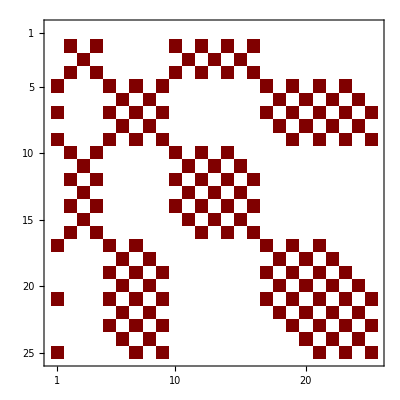

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/140 (-70 ⅈ-280 invPe+stEff (7-3 Λ) Λ) | 0 | 1/20 (-6 ⅈ+stEff (-5+Λ)) Λ | 0 | 0 | 0 | 0 | 0 | -√(3/70) (-ⅈ+stEff) Λ | 0 | (stEff (3-2 Λ) Λ)/(15 √14) | 0 | (Λ (-ⅈ+stEff Λ))/(5 √14) | 0 | 1/3 √(5/42) stEff Λ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 invPe+1/70 stEff Λ (-7+3 Λ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((2 ⅈ+stEff (-1+Λ)) Λ)/(2 √70) | 0 | -(stEff (-9+Λ) Λ)/(30 √21) | 0 | ((-2 ⅈ+stEff (-1+Λ)) Λ)/(2 √70) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/20 (6 ⅈ+stEff (-5+Λ)) Λ | 0 | 1/140 (70 ⅈ-280 invPe+stEff (7-3 Λ) Λ) | 0 | 0 | 0 | 0 | 0 | 1/3 √(5/42) stEff Λ^2 | 0 | (Λ (ⅈ+stEff Λ))/(5 √14) | 0 | (stEff (3-2 Λ) Λ)/(15 √14) | 0 | -√(3/70) (ⅈ+stEff) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-((-6 ⅈ+stEff (-5+Λ)) Λ)/(2 √30) | 0 | 0 | 0 | -6 invPe+1/42 (-42 ⅈ-stEff (-3+Λ) Λ) | 0 | -(Λ (6 ⅈ+stEff (7+Λ)))/(14 √6) | 0 | -(5 stEff Λ^2)/21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 (-ⅈ+stEff) Λ)/(√21) | 0 | (stEff (11-6 Λ) Λ)/(77 √3) | 0 | 1/7 √(2/15) Λ (-ⅈ+stEff Λ) | 0 | 1/77 √3 stEff Λ^2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/84 (-42 ⅈ-504 invPe-stEff Λ (3+Λ)) | 0 | 1/28 (-6 ⅈ+stEff (-5+Λ)) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((4 ⅈ+stEff (-3+Λ)) Λ)/(2 √42) | 0 | (stEff (22-9 Λ) Λ)/(77 √6) | 0 | (Λ (-4 ⅈ+stEff (-1+3 Λ)))/(14 √6) | 0 | 1/11 √(3/14) stEff Λ^2 | 0
(stEff Λ (-7+3 Λ))/(14 √5) | 0 | 0 | 0 | 1/14 √(3/2) (2 ⅈ+stEff (-1+Λ)) Λ | 0 | 1/14 (-84 invPe+stEff (-1+Λ) Λ) | 0 | 1/14 √(3/2) (-2 ⅈ+stEff (-1+Λ)) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 √(2/7) stEff Λ^2 | 0 | ((2 ⅈ+stEff (-1+Λ)) Λ)/(7 √2) | 0 | (2 stEff (11-4 Λ) Λ)/(77 √5) | 0 | ((-2 ⅈ+stEff (-1+Λ)) Λ)/(7 √2) | 0 | 1/11 √(2/7) stEff Λ^2
0 | 0 | 0 | 0 | 0 | 1/28 (6 ⅈ+stEff (-5+Λ)) Λ | 0 | 1/84 (42 ⅈ-504 invPe-stEff Λ (3+Λ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 √(3/14) stEff Λ^2 | 0 | (Λ (4 ⅈ+stEff (-1+3 Λ)))/(14 √6) | 0 | (stEff (22-9 Λ) Λ)/(77 √6) | 0 | ((-4 ⅈ+stEff (-3+Λ)) Λ)/(2 √42) | 0
-((6 ⅈ+stEff (-5+Λ)) Λ)/(2 √30) | 0 | 0 | 0 | -(5 stEff Λ^2)/21 | 0 | -(Λ (-6 ⅈ+stEff (7+Λ)))/(14 √6) | 0 | -6 invPe+1/42 (42 ⅈ-stEff (-3+Λ) Λ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/77 √3 stEff Λ^2 | 0 | 1/7 √(2/15) Λ (ⅈ+stEff Λ) | 0 | (stEff (11-6 Λ) Λ)/(77 √3) | 0 | -(2 (ⅈ+stEff) Λ)/(√21)
0 | -1/2 √(3/70) (-8 ⅈ+stEff (-7+Λ)) Λ | 0 | √(5/42) stEff Λ^2 | 0 | 0 | 0 | 0 | 0 | -(3 ⅈ)/2-12 invPe+1/132 stEff (11-3 Λ) Λ | 0 | -(Λ (2 ⅈ+stEff (3+Λ)))/(4 √15) | 0 | -1/11 √(5/3) stEff Λ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -((-4 ⅈ+stEff (-3+Λ)) Λ)/(√70) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ-12 invPe-(stEff Λ^2)/33 | 0 | -(Λ (6 ⅈ+stEff (7+Λ)))/(6 √30) | 0 | -(5 stEff Λ^2)/33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (stEff (-4+Λ) Λ)/(5 √14) | 0 | -(Λ (-8 ⅈ+stEff (-5+3 Λ)))/(10 √14) | 0 | 0 | 0 | 0 | 0 | (Λ (6 ⅈ+stEff (-1+5 Λ)))/(12 √15) | 0 | -12 invPe+1/660 (-330 ⅈ+stEff Λ (-33+17 Λ)) | 0 | 1/30 (-6 ⅈ+stEff (-5+Λ)) Λ | 0 | -1/11 √(5/3) stEff Λ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 stEff Λ (-3+2 Λ))/(5 √21) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((2 ⅈ+stEff (-1+Λ)) Λ)/(2 √30) | 0 | -12 invPe+1/165 stEff Λ (-11+9 Λ) | 0 | ((-2 ⅈ+stEff (-1+Λ)) Λ)/(2 √30) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(Λ (8 ⅈ+stEff (-5+3 Λ)))/(10 √14) | 0 | (stEff (-4+Λ) Λ)/(5 √14) | 0 | 0 | 0 | 0 | 0 | -1/11 √(5/3) stEff Λ^2 | 0 | 1/30 (6 ⅈ+stEff (-5+Λ)) Λ | 0 | -12 invPe+1/660 (330 ⅈ+stEff Λ (-33+17 Λ)) | 0 | (Λ (-6 ⅈ+stEff (-1+5 Λ)))/(12 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -((4 ⅈ+stEff (-3+Λ)) Λ)/(√70) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(5 stEff Λ^2)/33 | 0 | -(Λ (-6 ⅈ+stEff (7+Λ)))/(6 √30) | 0 | ⅈ-12 invPe-(stEff Λ^2)/33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √(5/42) stEff Λ^2 | 0 | -1/2 √(3/70) (8 ⅈ+stEff (-7+Λ)) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/11 √(5/3) stEff Λ^2 | 0 | -(Λ (-2 ⅈ+stEff (3+Λ)))/(4 √15) | 0 | (3 ⅈ)/2-12 invPe+1/132 stEff (11-3 Λ) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/3 √(10/7) stEff Λ^2 | 0 | 0 | 0 | -((-10 ⅈ+stEff (-9+Λ)) Λ)/(2 √21) | 0 | 17/33 √(2/7) stEff Λ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ-20 invPe-1/143 stEff Λ (-13+3 Λ) | 0 | -(Λ (6 ⅈ+stEff (11+5 Λ)))/(22 √7) | 0 | -9/143 √(10/7) stEff Λ^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -((-5 ⅈ+stEff (-4+Λ)) Λ)/(√42) | 0 | (17 stEff Λ^2)/(11 √42) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -20 invPe+1/572 (-858 ⅈ+stEff (13-21 Λ) Λ) | 0 | -(9 Λ (2 ⅈ+stEff (3+Λ)))/(44 √7) | 0 | -(45 stEff Λ^2)/(143 √7) | 0 | 0 | 0
0 | 0 | 0 | 0 | (stEff Λ (-55+9 Λ))/(154 √3) | 0 | -(Λ (-10 ⅈ+stEff (-7+3 Λ)))/(14 √2) | 0 | (17 stEff Λ^2)/(77 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (Λ (6 ⅈ+stEff+7 stEff Λ))/(22 √7) | 0 | -ⅈ-20 invPe-(stEff Λ (26+3 Λ))/1001 | 0 | -3/154 √(5/2) Λ (6 ⅈ+stEff (7+Λ)) | 0 | -(135 stEff Λ^2)/1001 | 0 | 0
0 | 0 | 0 | 0 | 0 | (stEff Λ (-55+26 Λ))/(77 √6) | 0 | -(Λ (-5 ⅈ+stEff (-3+2 Λ)))/(7 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 Λ (6 ⅈ+stEff (-1+5 Λ)))/(44 √7) | 0 | -20 invPe+(-2002 ⅈ+stEff Λ (-221+141 Λ))/4004 | 0 | 5/154 (-6 ⅈ+stEff (-5+Λ)) Λ | 0 | -(45 stEff Λ^2)/(143 √7) | 0
(2 stEff Λ^2)/21 | 0 | 0 | 0 | -1/14 √(5/6) (2 ⅈ+stEff (-1+Λ)) Λ | 0 | 1/231 √5 stEff Λ (-33+19 Λ) | 0 | -1/14 √(5/6) (-2 ⅈ+stEff (-1+Λ)) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9/143 √(10/7) stEff Λ^2 | 0 | 9/154 √(5/2) (2 ⅈ+stEff (-1+Λ)) Λ | 0 | -20 invPe+(stEff Λ (-65+51 Λ))/1001 | 0 | 9/154 √(5/2) (-2 ⅈ+stEff (-1+Λ)) Λ | 0 | -9/143 √(10/7) stEff Λ^2
0 | 0 | 0 | 0 | 0 | -(Λ (5 ⅈ+stEff (-3+2 Λ)))/(7 √6) | 0 | (stEff Λ (-55+26 Λ))/(77 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(45 stEff Λ^2)/(143 √7) | 0 | 5/154 (6 ⅈ+stEff (-5+Λ)) Λ | 0 | -20 invPe+(2002 ⅈ+stEff Λ (-221+141 Λ))/4004 | 0 | (3 Λ (-6 ⅈ+stEff (-1+5 Λ)))/(44 √7) | 0
0 | 0 | 0 | 0 | (17 stEff Λ^2)/(77 √3) | 0 | -(Λ (10 ⅈ+stEff (-7+3 Λ)))/(14 √2) | 0 | (stEff Λ (-55+9 Λ))/(154 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(135 stEff Λ^2)/1001 | 0 | -3/154 √(5/2) Λ (-6 ⅈ+stEff (7+Λ)) | 0 | ⅈ-20 invPe-(stEff Λ (26+3 Λ))/1001 | 0 | (Λ (-6 ⅈ+stEff+7 stEff Λ))/(22 √7)
0 | 0 | 0 | 0 | 0 | (17 stEff Λ^2)/(11 √42) | 0 | -((5 ⅈ+stEff (-4+Λ)) Λ)/(√42) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(45 stEff Λ^2)/(143 √7) | 0 | -(9 Λ (-2 ⅈ+stEff (3+Λ)))/(44 √7) | 0 | -20 invPe+1/572 (858 ⅈ+stEff (13-21 Λ) Λ) | 0
-1/3 √(10/7) stEff Λ^2 | 0 | 0 | 0 | 0 | 0 | 17/33 √(2/7) stEff Λ^2 | 0 | -((10 ⅈ+stEff (-9+Λ)) Λ)/(2 √21) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9/143 √(10/7) stEff Λ^2 | 0 | -(Λ (-6 ⅈ+stEff (11+5 Λ)))/(22 √7) | 0 | 2 ⅈ-20 invPe-1/143 stEff Λ (-13+3 Λ))

```mathematica
maxl=4;
sparsetest = assemblesparse[maxl];
ByteCount[sparsetest]
MatrixPlot[sparsetest]
MatrixForm[sparsetest]
```

## Augmented matrix, even l,m

Here we’ll save the real and imaginary parts of c_lm as separate elements, so if we want to we can export from mathematica and use any sparse solver we like.

sparseindex[l,m] gives the index of the real part of c_lm, the imaginary is the next index

```mathematica
sparseindex[l_Integer,m_Integer]:=m+(l/2)^2-(-1+m) KroneckerDelta[0,m]/;EvenQ[l]&&EvenQ[m];
(* Computed from: sparseindex[l_,m_]:= 1 + Sum[1+k,{k,0,l-2,2}]+(1-KroneckerDelta[m,0])(m-1); *)
```

These are the functions that do the actual assembling.

```mathematica
AppendRules[list_,pos_->val_]:=Module[{},
existingpos=Position[list,pos->_];
If[Length[existingpos]==0,
Append[list,pos->val],

existingpos=existingpos[[1,1]];
existingrule = list[[existingpos]];
newrule = existingrule /.(pos->x_):>(pos->x+val);
ReplacePart[list,existingpos->newrule]
]
];
assemblesparseoptimised[maxl_]:=Module[{row,p,q,col,dl,dm,l2,m2,sparserules,value,size,k,delta,temprules,m2sign,m2magn,recol,imcol,revalue,imvalue},
size =sparseindex[maxl,maxl]+1;
Print[size];
row=1;
sparserules={};
For[p=0,p<=maxl,p+=2,
For[q=0,q≤p,q+=2,
temprules = {};
For[k=1,k≤Length[matrixelements],k++,
delta=matrixelements[[k,1]];
dl=delta[[1]];
dm=delta[[2]];
l2=p-dl;
m2 = q-dm;
m2sign = Sign[m2];
m2magn=Abs[m2];
If [l2≥0 && l2≤maxl&&Abs[m2]≤l2,
recol = sparseindex[l2,m2magn];
imcol = recol+1;
value=Simplify[ matrixelements[[k,2]]/.{l->l2,m->m2}];
revalue=Simplify[Re[value],{Λ∈Reals,invPe∈Reals,stEff∈Reals}];
imvalue=Simplify[Im[value],{Λ∈Reals,invPe∈Reals,stEff∈Reals}];
(*Row for real value*)

If[Not[revalue===0],
temprules=AppendRules[temprules,{row,recol}->revalue];
];
If[Not[imvalue===0]&&Not[m2==0],
temprules=AppendRules[temprules,{row,imcol}->-imvalue m2sign];
];
(*Row for imaginory value*)
If[Not[q==0],
If[Not[revalue===0]&&Not[m2==0],
temprules=AppendRules[temprules,{row+1,imcol}->revalue m2sign];
];
If[Not[imvalue===0],
temprules=AppendRules[temprules,{row+1,recol}->imvalue];
];
];

];
];
sparserules = Join[sparserules,temprules];
row+=If[q==0,1,2];
];
PrintTemporary[p]
];

SparseArray[sparserules]
]/;EvenQ[maxl];
```

## Test it

49

356784

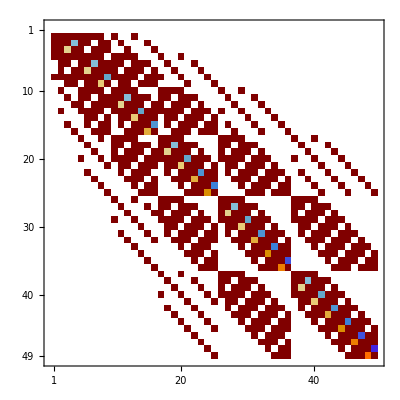

```mathematica
maxl=12;
sparsetest = assemblesparseoptimised[maxl];
ByteCount[sparsetest]
MatrixPlot[sparsetest]
(*MatrixForm[sparsetest]*)
```

## Assemble up to some size, and save it to a .mx file (platform specific, dont transfer .mx around)

```mathematica
maxl = 400;
sparseOptimised=assemblesparseoptimised[maxl]
sparseAugmented = sparseOptimised[[2;;,2;;]];
augmentedB=-sparseOptimised[[2;;,1]] * 1/(2 Sqrt[Pi])//Normal;
DumpSave[ToString[StringForm["augmentedMatrix_lmax``.mx",maxl]],{sparseAugmented,augmentedB}];
```

10201

SparseArray[<275933>,{10201,10201}]

{SparseArray[<275928>,{10200,10200}],{-(stEff Λ (-7+3 Λ))/(28 √(5 π)),(stEff (-5+Λ) Λ)/(4 √(30 π)),1/2 √(3/(10 π)) Λ,-(stEff Λ^2)/(21 √π),0,0,1/3 √(5/(14 π)) stEff Λ^2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## See if it works

```mathematica
Clear[sparseAugmented,augmentedB]
Get[ToString[StringForm["augmentedMatrix_lmax``.mx",maxl]]]
Dimensions[sparseAugmented]
MatrixPlot[sparseAugmented]
```